```mathematica
n=10;
α=.01;
β=0;
```

```mathematica
Q[0]=Table[RandomInteger[{1,1000}],{i,1,n}]
```

{465,278,789,897,583,356,713,808,590,893}

```mathematica
x=Table[{RandomReal[{0,100}],RandomReal[{0,100}]},{i,1,n}];
d=Table[EuclideanDistance[x[[i]],x[[j]]],{i,1,n},{j,1,n}];
```

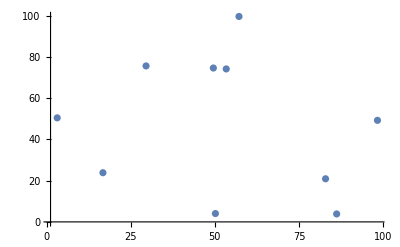

```mathematica
ListPlot[x,PlotRange->All]
```

```mathematica
M1[Q_]:=α*Table[If[j≠i,Boole[Q[[j]]<Q[[i]]]/d[[i,j]],0],{i,1,n},{j,1,n}]
M2[Q_]:=-α*Table[If[j==i,Sum[If[k≠i,Boole[Q[[k]]>Q[[i]]]/d[[i,k]],0],{k,1,n}],0],{i,1,n},{j,1,n}]
M3[Q_]:=β*IdentityMatrix[n]
```

```mathematica
M[Q_]:=M1[Q]+M2[Q]+M3[Q]
```

```mathematica
TraditionalForm[M[Q[0]]]
```

(-0.00382544 | 0.000128816 | 0. | 0. | 0. | 0.000419036 | 0. | 0. | 0. | 0.
0. | -0.00177247 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.000388527 | 0.0000998877 | -0.000619492 | 0. | 0.000153712 | 0.00027333 | 0.000136889 | 0. | 0.000104302 | 0.
0.00259514 | 0.000125447 | 0.000382389 | 0. | 0.000181924 | 0.000499562 | 0.000191168 | 0.000165371 | 0.000141633 | 0.00015815
0.0001946 | 0.000212732 | 0. | 0. | -0.00101904 | 0.000135792 | 0. | 0. | 0. | 0.
0. | 0.000109348 | 0. | 0. | 0. | -0.0020542 | 0. | 0. | 0. | 0.
0.000180039 | 0.000105021 | 0. | 0. | 0.000105092 | 0.00027408 | -0.000780216 | 0. | 0.000151365 | 0.
0.000160584 | 0.000138388 | 0.000116389 | 0. | 0.000117054 | 0.000187362 | 0.00033455 | -0.000316417 | 0.000257451 | 0.
0.000142378 | 0.000277595 | 0. | 0. | 0.000151393 | 0.000134192 | 0. | 0. | -0.000926352 | 0.
0.000164167 | 0.000575233 | 0.000120715 | 0. | 0.000309868 | 0.000130849 | 0.000117609 | 0.000151046 | 0.000271601 | -0.00015815)

```mathematica
Eigenvalues[M[Q[0]]]
```

{-0.00382544,-0.0020542,-0.00177247,-0.00101904,-0.000926352,-0.000780216,-0.000619492,-0.000316417,-0.00015815,0.}

```mathematica
Q[t_]=FullSimplify[MatrixExp[t*M[Q[0]]].Q[0]];
```

```mathematica
Limit[Q[t],t->Infinity]
```

{-4.40168×10^-15,5.04529×10^-13,7.39743×10^-13,6372.,-1.90892×10^-13,-2.37194×10^-13,7.37986×10^-13,-1.41662×10^-12,7.14391×10^-13,-1.52505×10^-12}

```mathematica
Manipulate[ListPlot[Reverse[Sort[N[Q[t]]]],PlotRange->All],{t,0,10000,.1}]
```

```mathematica
findRankSwitch[max_]:=Module[{T={0},t0=0,delT=.1},

While[t0≤max,
If[!DuplicateFreeQ[Round[Q[t0],.01]]&&DuplicateFreeQ[Round[Q[t0+delT],.01]],
AppendTo[T,Last[T]+t0];
Q[t_]=FullSimplify[MatrixExp[t*M[Q[t0]]].Q[t0]];
t0=0;
];
t0+=delT;
];
Return[T];
]
```

```mathematica
findRankSwitch[1000]
```

{0,333.2}

```mathematica
Q[t_]=FullSimplify[MatrixExp[t*M[Q[10.1]]].Q[10.1]];
```

```mathematica
Sort[Q[330.5-320.2]]
```

{140.867,149.315,180.414,444.727,486.95,625.505,766.961,934.422,1122.2,1520.64}

```mathematica
Sort[Q[310.1]]
```

{37.9664,93.4911,120.932,343.146,400.95,541.751,710.346,992.221,1259.56,1871.63}